# Geometric structure of thermal cones

```mathematica
Clear["Global`*"]
```

#### In this notebook, we provide a code to construct the thermal cones for an energy-incoherent state p, with Hamiltonian H, interacting with a heat bath at inverse temperature β.

## List of functions

All functions used to construct the thermal cones or obtain some of their properties are listed below. Almost all commands are illustrated in the Examples.

```mathematica
projection[x_]:=#⟦;;-2⟧/(2+#⟦-1⟧)&[(x )]; 

funcFromPoints[points_]:=Piecewise[{((#[[1,2]]-#[[2,2]])/(#[[1,1]]-#[[2,1]]))(x-#[[1,1]])+#[[1,2]],Max[#[[;;,1]]]≥x>Min[#[[;;,1]]]}&/@Subsequences[Sort[points],{2}]]

probabilityFunc[x_,ps_,Es_:{1,1,1},β_:0]:=Module[{order,accum,tmp1,tmp2,γ},
γ=Exp[β Es];
order=Ordering[-γ ps];
γ=Exp[-β Es][[order]];
accum=Prepend[Accumulate[Normalize[ps[[order]],Total]],0];
Piecewise[{{accum[[1]] x,x≤ 1}}];
tmp2=Subsequences[Prepend[Accumulate[γ],0],{2}];
tmp1=Subsequences[accum,{2}];Piecewise[Table[{((#1[[2]]-#1[[1]])/(#2[[2]]-#2[[1]]))(x-tmp2[[i,1]])+#1[[1]]&[tmp1[[i]],tmp2[[i]]],x≤Accumulate[γ][[i]]},{i,1,Length[tmp1]}]]]

rot[d_]:=Reverse/@Table[Normalize[PadLeft[Flatten[{n,Table[-1,n]}],d]],{n,1,d-1}]

γs[Es_,β_]:=Exp[-Es β];

GibbsState[Es_,β_]:=Normalize[γs[Es,β],Total]; 

βorder[p_,Es_,β_]:=Ordering[-p/γs[Es,β]];

ThermoMajorizationCurve[p_,Es_,β_]:=Module[{opvec,oγs},
opvec=p⟦βorder[p,Es,β]⟧;
oγs=γs[Es,β]⟦βorder[p,Es,β]⟧;
Prepend[Accumulate[Transpose[{oγs,opvec}]],{0,0}]]

ExtremePointsF[p_,Es_,β_]:=Module[{allorders,revorders},
allorders=Permutations[Range[Length[p]]];
revorders=Permute[Range[Length[p]],FindPermutation[#,Range[Length[p]]]]&/@allorders;
Table[Differences[Prepend[Table[funcFromPoints[ThermoMajorizationCurve[p,Es,β]]/.x->i,{i,Accumulate[γs[Es,β]⟦allorders⟦j⟧⟧]}],0]]⟦revorders⟦j⟧⟧,{j,1,Length[p]!}]]

FutureThermalConeRaw[p_,Es_,β_]:=ConvexHullMesh[rot[Length[p]].#&/@ExtremePointsF[p,Es,β]];

FutureThermalCone[p_,Es_,β_]:= If[Length[p]>3,
Graphics3D[{FaceForm[Opacity[0.45,RGBColor["#91FF85"]]],EdgeForm[{Thick,RGBColor["#437F3B"]}],ConvexHullMesh[rot[Length[p]].#&/@ExtremePointsF[p,Es,β]]},Boxed->False],Graphics[{FaceForm[Opacity[0.45,RGBColor["#91FF85"]]],EdgeForm[{Thick,RGBColor["#437F3B"]}],ConvexHullMesh[rot[Length[p]].#&/@ExtremePointsF[p,Es,β]]}]]

tvectors[p_,Es_,β_,perm_]:=Module[{γ,βO,revorders},
γ=Exp[-β Es];
βO =Reverse@Ordering[p Exp[β Es]];
Table[
Append[#,1-Total[#]]&[
Flatten[{
Sum[p⟦βO⟧⟦k⟧,{k,1,j-1}]-(p⟦βO⟧⟦j⟧)/(γ⟦βO⟧⟦j⟧)(Sum[γ⟦βO⟧⟦k⟧,{k,1,j-1}]-γ⟦perm⟧⟦1⟧),
Table[(p⟦βO⟧⟦j⟧)/(γ⟦βO⟧⟦j⟧)γ⟦perm⟧⟦k⟧,
{k,2,Length[p]-1}]}]]⟦InversePermutation[perm]⟧,
{j,1,Length[p]}]]

Alltvectors[p_,Es_,β_]:=Module[{γ,βO,allorders,revorders},
γ=Exp[-β Es];
βO =Reverse@Ordering[p Exp[β Es]];
allorders=Permutations[Range[Length[p]]];
revorders=Permute[Range[Length[p]],FindPermutation[#,Range[Length[p]]]]&/@allorders;
Table[Append[#,1-Total[#]]&[
Flatten[{
Sum[p⟦βO⟧⟦k⟧,{k,1,j-1}]-(p⟦βO⟧⟦j⟧)/(γ⟦βO⟧⟦j⟧)(Sum[γ⟦βO⟧⟦k⟧,{k,1,j-1}]-γ⟦allorders⟦i⟧⟧⟦1⟧),
Table[(p⟦βO⟧⟦j⟧)/(γ⟦βO⟧⟦j⟧)γ⟦allorders⟦i⟧⟧⟦k⟧,
{k,2,Length[p]-1}]}]]⟦revorders⟦i⟧⟧,
{j,1,Length[p]},{i,1,Length[allorders]}]]

SetT[p_,Es_,β_]:=Module[{perms},
perms= Permutations[Range[Length[p]]];
RegionUnion[Table[RegionUnion[Table[ConvexHullMesh[rot[Length[p]].#&/@Union[ExtremePointsF[tvectors[p,Es,β,perms⟦k⟧]⟦j⟧,Es,β],ExtremePointsF[tvectors[p,Es,β,perms⟦k⟧]⟦j+1⟧,Es,β]]],{j,1,2}]],{k,1,Length[p]!}]]]

IncomparableRegionRaw[p_,Es_,β_]:=Module[{t},
t=Transpose[Alltvectors[p,Es,β]];
If[Length[p]>3,RegionIntersection[ReplacePart[Table[ConvexHullMesh[DeleteDuplicates[Flatten[Table[{rot[Length[p]].#&/@ExtremePointsF[t[[i,j]],Es,β],rot[Length[p]].#&/@ExtremePointsF[t[[i,j+1]],Es,β]},{i,1,Length[p]!}],2]]],{j,1,Length[p]-1}],0->RegionUnion],ConvexHullMesh[If[Length[p]>4,Nest[projection,#,Length[p]-4],#]&[rot[Length[p]].#]&/@IdentityMatrix[Length[p]]]],RegionIntersection[RegionDifference[SetT[p,Es,β],ConvexHullMesh[rot[Length[p]].#&/@ExtremePointsF[p,Es,β]]],ConvexHullMesh[rot[Length[p]].#&/@ExtremePointsF[Table[KroneckerDelta[1,i],{i,1,Length[p]}],Es,0]]]]]

PastThermalConeRaw[p_,Es_,β_]:=Module[{t},t=Transpose[Alltvectors[p,Es,β]];
If[Length[p]>3,RegionDifference[ConvexHullMesh[rot[Length[p]].#&/@ExtremePointsF[Table[KroneckerDelta[1,i],{i,1,Length[p]}],Es,0]],IncomparableRegionRaw[p,Es,β],PlotTheme->"Polygons"],RegionDifference[ConvexHullMesh[rot[Length[p]].#&/@ExtremePointsF[Table[KroneckerDelta[1,i],{i,1,Length[p]}],Es,0]],SetT[p,Es,β]]]]

IncomparableThermalRegion[p_,Es_,β_,opacity_:{0.5}]:=Module[{t},
t=Transpose[Alltvectors[p,Es,β]];
If[Length[p]>3,Graphics3D[{FaceForm[{Opacity[opacity],RGBColor[0.94,0.5,0.5]}],EdgeForm[{Thick,Darker[Red]}],IncomparableRegionRaw[p,Es,β]},Boxed->False],Graphics[{FaceForm[Opacity[0.45,RGBColor["#FD0000"]]],EdgeForm[{Thick,RGBColor["#9B4B4B"]}],IncomparableRegionRaw[p,Es,β]}]]]

PastThermalCone[p_,Es_,β_,opacity_:{0.5}]:=If[Length[p]>3,Graphics3D[{FaceForm[Opacity[opacity,RGBColor[0.55,0.58,0.85]]],EdgeForm[{Thick,RGBColor["#7078CF"]}], PastThermalConeRaw[p,Es,β]},Boxed->False],Graphics[{FaceForm[Opacity[0.2,RGBColor["#0000FA"]]],EdgeForm[{Thick,RGBColor["#7078CF"]}], PastThermalConeRaw[p,Es,β]}]]

Chambers[Es_,β_]:=ConvexHullMesh[#]&/@ Table[rot[Length[Es]].#&/@Table[Normalize[ReplacePart[γs[Es,β],(#->0&/@i)[[;;j]]],Total],{j,0,Length[Es]-1}],{i,Permutations[Range[Length[Es]]]}]

Chambersϵ[Es_,β_,ϵ_:10^-6]:=ConvexHullMesh[#]&/@ Table[rot[Length[Es]].#&/@Table[Normalize[ReplacePart[γs[Es,β],(#->0&/@i)[[;;j]]]-ϵ If[j==0,ReplacePart[γs[Es,β],(#->0&/@i)[[;;Length[Es]-1]]],0],Total],{j,0,Length[Es]-1}],{i,Permutations[Range[Length[Es]]]}]

ChamberEdges[Es_,β_]:=Module[{d},
d=Length[Es];
If[d>3,
Graphics3D[{{Table[{Dashing[Medium],Line[{
If[d>4,Nest[projection,#,d-4],#]&[rot[Length[Es]].Normalize[ReplacePart[γs[Es,β],i->0],Total]],
If[d>4,Nest[projection,#,d-4],#]&[rot[Length[Es]].IdentityMatrix[d][[i]]]}]},{i,1,d}]}},Boxed->False],Graphics[{{Table[{Dashing[Medium],Line[{
If[d>4,Nest[projection,#,d-4],#]&[rot[Length[Es]].Normalize[ReplacePart[γs[Es,β],i->0],Total]],
If[d>4,Nest[projection,#,d-4],#]&[rot[Length[Es]].IdentityMatrix[d][[i]]]}]},{i,1,d}]}}]]]

ThermalCones[p_,Es_,β_]:=
If[Length[p]>3,Show[IncomparableThermalRegion[p,Es,β,0.5],PastThermalCone[p,Es,β,0.3],FutureThermalCone[p,Es,β],ChamberEdges[Es,β],Graphics3D[{If[β==0,{Text[Style["(1,0,0,0)",20,Black,FontFamily->"Times"],rot[Length[p]].{1.12,0.05,0,0}],Text[Style["(0,1,0,0)",20,Black,FontFamily->"Times"],rot[Length[p]].{0.05,1.12,0,0}],Text[Style["(0,0,1,0)",20,Black,FontFamily->"Times"],rot[Length[p]].{0,0,1.05,0}],Text[Style["(0,0,0,1)",20,Black,FontFamily->"Times"],rot[Length[p]].{0,0,0,1.05}]},{Text[Style["E_1",20,Black,FontFamily->"Times"],rot[Length[p]].{1.13,0,0,0}],Text[Style["E_2",20,Black,FontFamily->"Times"],rot[Length[p]].{0,1.13,0,0}],Text[Style["E_3",20,Black,FontFamily->"Times"],rot[Length[p]].{0,0,1.35,0}],Text[Style["E_4",20,Black,FontFamily->"Times"],rot[Length[p]].{0,0,0,1.13}]}],{Text[Style["★",20,RGBColor["#3A3A3A"]],rot[Length[Es]].Normalize[γs[Es,β],Total]],{Opacity[.001],Sphere[{0,0,0},Sqrt[3/4]]}}}],PlotLabel->Style["β= "<> ToString[NumberForm[β,{4,1}]],{25,Black,FontFamily->"Times"}],ImageSize->500,Boxed->False],
If[β<=6,Show[IncomparableThermalRegion[p,Es,β],PastThermalCone[p,Es,β],FutureThermalCone[p,Es,β],ChamberEdges[Es,β],Graphics[{{PointSize[.016],RGBColor["#3A3A3A"],Point[rot[Length[Es]].p]},{Text[Style["★",20,RGBColor["#3A3A3A"]],rot[Length[Es]].Normalize[γs[Es,β],Total]]},If[β==0,{Text[Style["(1,0,0)",20,Black,FontFamily->"Times"],rot[Length[p]].{1.12,0.05,0}],Text[Style["(0,1,0)",20,Black,FontFamily->"Times"],rot[Length[p]].{0.05,1.12,0}],Text[Style["(0,0,1)",20,Black,FontFamily->"Times"],rot[Length[p]].{0,0,1.05}]},{Text[Style["E_1",20,Black,FontFamily->"Times"],rot[Length[p]].{1.07,0,0}],Text[Style["E_2",20,Black,FontFamily->"Times"],rot[Length[p]].{0,1.07,0}],Text[Style["E_3",20,Black,FontFamily->"Times"],rot[Length[p]].{0,0,1.05}]}]}],ImageSize->500,PlotLabel->Style["β= "<> ToString[NumberForm[β,{4,1}]],{25,Black,FontFamily->"Times"}]],Show[IncomparableThermalRegion[p,Es,6],PastThermalCone[p,Es,6],FutureThermalCone[p,Es,6],ImageSize->500]]]

PastThermalConeChambers[p_,Es_,β_,i_]:=If[Length[p]>3,Graphics3D[{FaceForm[Opacity[1,RGBColor[0.64,0.69,0.98]]],EdgeForm[{Thick,RGBColor["#7078CF"]}],RegionIntersection[PastThermalConeRaw[p,Es,β],Chambersϵ[Es,β,10^-3]⟦i⟧]},Boxed->False],
Graphics[{FaceForm[Opacity[0.2,RGBColor["#0000FA"]]],EdgeForm[{Thick,RGBColor["#7078CF"]}],RegionIntersection[PastThermalConeRaw[p,Es,β],Chambersϵ[Es,β]⟦i⟧]}]]

IncomparableThermalRegionChambers[p_,Es_,β_,i_]:=If[Length[p]>3,Graphics3D[{FaceForm[Opacity[1,RGBColor[0.92,0.5,0.5]]],EdgeForm[{Thick,RGBColor["#9B4B4B"]}],RegionIntersection[IncomparableRegionRaw[p,Es,β],Chambersϵ[Es,β,10^-3]⟦i⟧]},Boxed->False],
Graphics[{FaceForm[Opacity[0.45,RGBColor["#FD0000"]]],EdgeForm[{Thick,RGBColor["#9B4B4B"]}],RegionIntersection[IncomparableRegionRaw[p,Es,β],Chambers[Es,β]⟦i⟧]}]]

FutureThermalConeChambers[p_,Es_,β_,i_]:=If[Length[p]>3,Graphics3D[{FaceForm[Opacity[1,RGBColor[0.5,0.87,0.5]]],EdgeForm[None],RegionIntersection[FutureThermalConeRaw[p,Es,β],Chambersϵ[Es,β,10^-3]⟦i⟧]},Boxed->False],Graphics[{FaceForm[Opacity[0.45,RGBColor["#91FF85"]]],EdgeForm[None],RegionIntersection[FutureThermalConeRaw[p,Es,β],Chambers[Es,β]⟦i⟧]}]]

ThermalConesChambers[p_,Es_,β_,i_]:=Show[PastThermalConeChambers[p,Es,β,i],IncomparableThermalRegionChambers[p,Es,β,i],FutureThermalConeChambers[p,Es,β,i]]
```

## Examples

⚠  Mathematica is not so smart when working with 'non-machine' numbers, i.e., integers. So to avoid any issue  β has to be a float number. For example β = 2.0 instead of β = 2. Moreover, Mathematica does not cope very well with 3D shapes and the package I’m using, so it may happen that for a four-level system and specific values of β some error will appear.

Although the name of each command is self-explanatory about their function, we now illustrate how to use them:

Code: ThermalCones[state, energies, β]

```mathematica
p={0.7,0.2,0.1};Es={0,1,2};β=0.5;
```

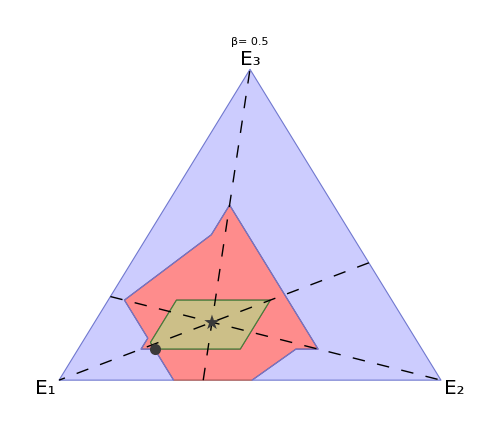

```mathematica
ThermalCones[p,Es,0.5]
```

The algorithm also works for a four-level system:

```mathematica
q={0.13,0.09,0.36,0.42};
```

```mathematica
ThermalCones[q,{0,1,2,4},0.5]
```

-Graphics3D-

Visualizing the evolution of the thermal cones by going from β = 0 to β → ∞:

```mathematica
ListAnimate[Table[ThermalCones[p,{0,1,2},β],{β,0,2,0.01}]]
```

To obtain the past and future thermal cones and the incomparable region separately, one can use the following codes:

Code: PastThermalCone[state, energies, β,], IncomparableRegion[state, energies, β,] and FutureThermalCone[state, energies, β,]

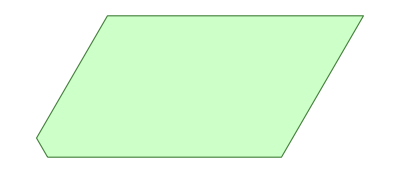

```mathematica
FutureThermalCone[p,Es,β]
```

```mathematica
FutureThermalCone[q,{0,1,2,3},β]
```

-Graphics3D-

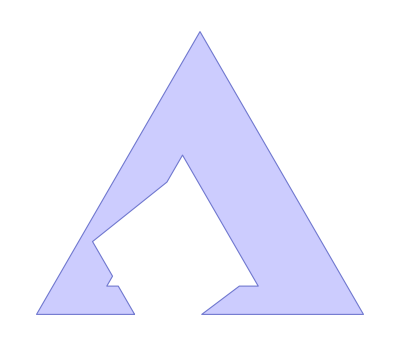

```mathematica
PastThermalCone[p,Es,β]
```

For a four-level system these plots are difficult to visualise due to their inner structure. In order to make their visualisation better, we add a way of controlling their opacity:  PastThermalCone[state, energies, β, opacity], IncomparableRegion[state, energies, β,opacity]

```mathematica
PastThermalCone[q,{0,1,2,3},0,1]
```

-Graphics3D-

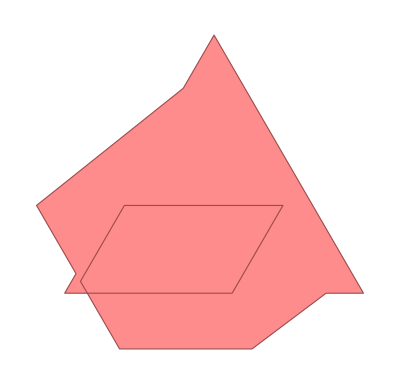

```mathematica
IncomparableThermalRegion[p,Es,β]
```

```mathematica
IncomparableThermalRegion[q,{0,1,2,3},0,1]
```

-Graphics3D-

To visualise them in each Weyl Chamber, we simply need to use the code: ThermalConesChambers[state, energies, β, chamber]

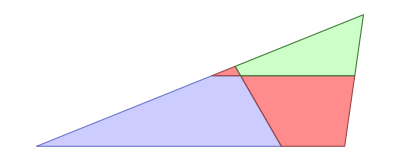

```mathematica
ThermalConesChambers[p,Es,β,6]
```

```mathematica
ThermalConesChambers[q,{0,1,2,3},0,1]
```

-Graphics3D-

To see them separately in each Weyl chamber, we use PastThermalConeChambers[state, energies, β, chamber], IncomparableThermalRegionChambers[state, energies, β, chamber] and FutureThermalConeChambers[state, energies, β, chamber]

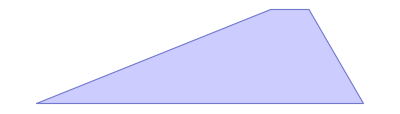

```mathematica
PastThermalConeChambers[p,Es,β,6]
```

```mathematica
PastThermalConeChambers[q,{0,1,2,3},β,1]
```

-Graphics3D-

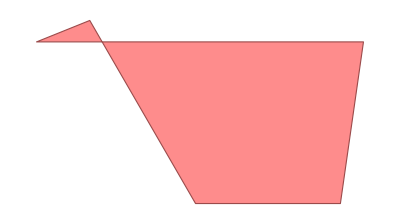

```mathematica
IncomparableThermalRegionChambers[p,Es,β,6]
```

```mathematica
IncomparableThermalRegionChambers[q,{0,1,2,3},β,1]
```

-Graphics3D-

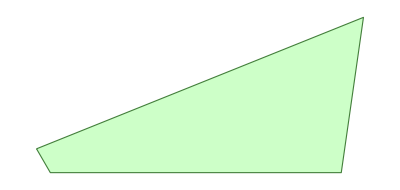

```mathematica
FutureThermalConeChambers[p,Es,β,6]
```

```mathematica
FutureThermalConeChambers[q,{0,1,2,3},β,1]
```

-Graphics3D-

These functions are enough to play around with thermal cones and understand their main behaviour.

## Extreme points for arbitrary dimension

For a d-dimensional energy-incoherent state, the set of extreme points of the future and past can be obtained by using the following:

Code: ExtremePointsF[state, energies, β,],  tvectors[state, energies, β, chamber]

## Example of usage:

For a 7-dimensional state:

```mathematica
test = Normalize[RandomReal[1,7],Total];
```

```mathematica
ExtremePointsF[test,Range[7],0.5]
```

```mathematica
tvectors[test,Range[7],0.5]
```